## Physics 430 Lab 2

### Problem 2.1 b

```mathematica
DSolve[{y''[x]+9 y[x]==Sin[x], y[0]==0,y[2]==1},y[x],x]//FullSimplify
```

{{y[x]→1/8 (Sin[x]-Csc[6] (-8+Sin[2]) Sin[3 x])}}

### Problem 2.2 b

{{y[x]→InterpolatingFunction[{{0., 5.}}, <>][x]}}

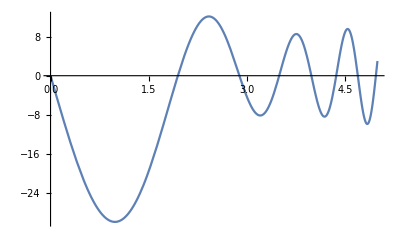

```mathematica
NDSolve[{y''[x]+Sin[x] y'[x]+Exp[x] y[x] == x^2, y[0]==0, y[5]==3},y[x],{x,0,5}]
y1[x_]=y[x]/.%[[1]][[1]];
Plot[y1[x],{x,0,5}]
```

```mathematica
y1[4.5]
```

8.72062

### Problem 2.3 b

```mathematica
Solve[yj1==a+b (x-2 h)+c (x-2 h)^2 && yj2==a+b (x-h)+c (x- h)^2 && yj3==a+b x+c x^2,{a,b,c}];
b/.%[[1]][[2]];
c/.%%[[1]][[3]];
D[a+b x+c x^2,x];
%/.b->%%%/.c->%%//FullSimplify
```

(yj1-4 yj2+3 yj3)/(2 h)

### Problem 2.4

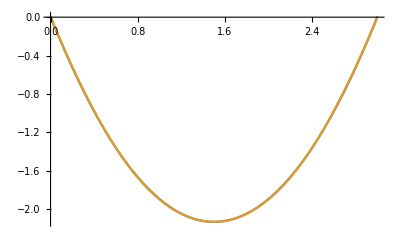

```mathematica
NDSolve[{y''[x]==1-Sin[y[x]],y[0]==0,y[3]==0},y[x],{x,0,3}];
y2[x_]=y[x]/.%[[1]][[1]];
Plot[{.95(x-1.5)^2-2.13,y2[x]},{x,0,3}]
```